```mathematica
names=FileNames["/Users/ranza/Projects/Quantum/QSF-examples/examples/argon-2e/Results/eberly/fwhm_cycles_6.000000/phase_0.000000/momenta_repX.psi*"]
```

{/Users/ranza/Projects/Quantum/QSF-examples/examples/argon-2e/Results/eberly/fwhm_cycles_6.000000/phase_0.000000/momenta_repX.psi0,/Users/ranza/Projects/Quantum/QSF-examples/examples/argon-2e/Results/eberly/fwhm_cycles_6.000000/phase_0.000000/momenta_repX.psi1,/Users/ranza/Projects/Quantum/QSF-examples/examples/argon-2e/Results/eberly/fwhm_cycles_6.000000/phase_0.000000/momenta_repX.psi2,/Users/ranza/Projects/Quantum/QSF-examples/examples/argon-2e/Results/eberly/fwhm_cycles_6.000000/phase_0.000000/momenta_repX.psi3}

```mathematica
names=FileNames["/Users/ranza/Projects/Quantum/QSF-examples/examples/argon-2e/Results/agh-transfergrid-es/fwhm_cycles_6.576000/phase_0.000000/momenta_scale8_repX.psi*"];
single=Select[names,StringEndsQ[#,"1"]||StringEndsQ[#,"2"]&];
```

```mathematica
WFHeader/@single
```

{<|dim→2,rep→1,isComplex→False,downscale→8,ns→{134217986,68719476736},dxs→{6.6312496×10^-316,3.395193266×10^-313},bounded→{2,1}|>,<|dim→2,rep→1,isComplex→False,downscale→8,ns→{134217986,68719476736},dxs→{6.6312496×10^-316,3.395193266×10^-313},bounded→{2,1}|>}

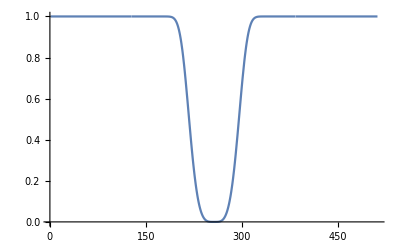

```mathematica
Plot[If[Abs[n/2-i]>n/4,1,1-Exp[- (i-n/2-0.5)^4 eta]],{i,1,n},PlotRange->Full]
```

```mathematica
n=512;
nCAP=n/4;
eta=Power[3.0/nCAP,4];
maska=ArrayPlot[Table[If[Abs[n/2-i]>n/4,1,(1-Exp[- (i-n/2-0.5)^4 eta])],{i,1,n},{j,1,n}],PlotLegends->Automatic,PlotRange->Full];
```

```mathematica
data=WFLoad /@single;
```

```mathematica
data[[1,2]]maska
```

$Aborted[]

```mathematica
ArrayPlot[Fourier/@(#[[2]]maska) ,ColorFunction->"Rainbow"]&/@data
```

Fourier::fftl: Argument {<<3292840240 bytes>>} is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of Fourier::fftl will be suppressed during this calculation.

$Aborted

{-Graphics-,-Graphics-}

$Aborted

{-Graphics-,-Graphics-}

```mathematica
names=FileNames["/Users/ranza/Projects/Quantum/QSF-examples/examples/argon-2e/Results/agh-transfergrid-es/fwhm_cycles_6.576000/phase_0.000000/momenta_scale8_repP.psi*"]
```

{/Users/ranza/Projects/Quantum/QSF-examples/examples/argon-2e/Results/agh-transfergrid-es/fwhm_cycles_6.576000/phase_0.000000/momenta_scale8_repP.psi0,/Users/ranza/Projects/Quantum/QSF-examples/examples/argon-2e/Results/agh-transfergrid-es/fwhm_cycles_6.576000/phase_0.000000/momenta_scale8_repP.psi1,/Users/ranza/Projects/Quantum/QSF-examples/examples/argon-2e/Results/agh-transfergrid-es/fwhm_cycles_6.576000/phase_0.000000/momenta_scale8_repP.psi2,/Users/ranza/Projects/Quantum/QSF-examples/examples/argon-2e/Results/agh-transfergrid-es/fwhm_cycles_6.576000/phase_0.000000/momenta_scale8_repP.psi3}

```mathematica
NotebookDirectory[]<>"common/wf.wls"
```

/Users/ranza/Projects/Quantum/QSF-examples/QSF/plotting/common/wf.wls

```mathematica
<<"/Users/ranza/Projects/Quantum/QSF-examples/QSF/plotting/common/wf.wls"
```

```mathematica
data=WFLoad /@Select[names,!StringEndsQ[#,"0"]&];
ArrayPlot[#[[2]] ,ColorFunction->"Rainbow"]&/@data
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot[Total[MapIndexed[If[First@#2<3,0.01,1]*#1&, data[[All,2]]] ], ColorFunction->"Rainbow"]
```

-Graphics-